# Brute-force classify

MSTに対して、CVI評価と最長エッジの削除を繰り返し、クラスタ数が1からNまでのCVIを得て、最良のCVIを持つクラシフィケーションを選択する。

必要なデータ: 
- 距離行列 (V * V)
- MST (2 * E)
- 連結行列(ノード同士が何ステップでつながっているか) (V * V)
- クラス分けリスト (V * V)

CVI:
CNS3 (mstPi2rkS[3] @ Cluster+Distance_Operations.txt)
CNS4 (mstPi2rkS[4] @ Cluster+Distance_Operations.txt)
Example - /Users/kouamano/gitsrc/ClusteringAdequation/ClusterValidityIndices_Sriparna_Exam(calc-index).nb

## 準備

```mathematica
$CharacterEncoding="UTF-8"
```

UTF-8

```mathematica
(*Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
(*Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]
```

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/Brute-force-classify"]*)
```

```mathematica
(*SetDirectory["/Users/amanokou/gitsrc/Brute-force-classify"]*)
```

```mathematica
SetDirectory["/home/kamano/gitsrc/Brute-force-classify"]
```

/home/kamano/gitsrc/Brute-force-classify

## 手順Example

データ:

```mathematica
data1={{0.7598461064538076,0.2762446676639849},{0.052506257778350385,0.4754933397861183},{0.835725205441473,0.971833104200341},{0.6256858201023905,0.39269853076870276},{0.8735494574667926,0.12663983198252038},{0.7508780147998599,0.6241170701623782},{0.2698064552281392,0.7247970742521272}}
```

{{0.759846,0.276245},{0.0525063,0.475493},{0.835725,0.971833},{0.625686,0.392699},{0.873549,0.12664},{0.750878,0.624117},{0.269806,0.724797}}

```mathematica
(*data1=Table[{RandomReal[],RandomReal[]},{7}]*)
```

距離行列:

```mathematica
(data1dmat=Outer[EuclideanDistance,data1,data1,1])//MatrixForm
```

(0. | 0.734867 | 0.699715 | 0.177653 | 0.18791 | 0.347988 | 0.664333
0.734867 | 0. | 0.927246 | 0.579128 | 0.892082 | 0.714011 | 0.330714
0.699715 | 0.927246 | 0. | 0.616047 | 0.846039 | 0.357918 | 0.617488
0.177653 | 0.579128 | 0.616047 | 0. | 0.363626 | 0.263111 | 0.486764
0.18791 | 0.892082 | 0.846039 | 0.363626 | 0. | 0.512379 | 0.849881
0.347988 | 0.714011 | 0.357918 | 0.263111 | 0.512379 | 0. | 0.491494
0.664333 | 0.330714 | 0.617488 | 0.486764 | 0.849881 | 0.491494 | 0.)

距離行列書き出し:

```mathematica
Export["data1.dmat",data1dmat,"TSV"]
```

data1.dmat

MST:

```mathematica
Run["/usr/local/bin/MST dmat=data1.dmat > data1.mst"]
```

0

MSTの読み込み:

```mathematica
(mst=Map[#+{1,1,0}&,Import["data1.mst","TSV"]])//TableForm
```

1 | 4 | 0.177653
1 | 5 | 0.18791
4 | 6 | 0.263111
6 | 3 | 0.357918
4 | 7 | 0.486764
7 | 2 | 0.330714

Plot:

:edge:

```mathematica
pos=Map[#[[{1,2}]]&,mst]
```

{{1,4},{1,5},{4,6},{6,3},{4,7},{7,2}}

:line coordinate:

```mathematica
cod=Map[data1[[#]]&,pos,{2}]
```

{{{0.759846,0.276245},{0.625686,0.392699}},{{0.759846,0.276245},{0.873549,0.12664}},{{0.625686,0.392699},{0.750878,0.624117}},{{0.750878,0.624117},{0.835725,0.971833}},{{0.625686,0.392699},{0.269806,0.724797}},{{0.269806,0.724797},{0.0525063,0.475493}}}

```mathematica
line=Map[Line[#]&,cod,{1}]
```

{Line[{{0.759846,0.276245},{0.625686,0.392699}}],Line[{{0.759846,0.276245},{0.873549,0.12664}}],Line[{{0.625686,0.392699},{0.750878,0.624117}}],Line[{{0.750878,0.624117},{0.835725,0.971833}}],Line[{{0.625686,0.392699},{0.269806,0.724797}}],Line[{{0.269806,0.724797},{0.0525063,0.475493}}]}

:Plot:

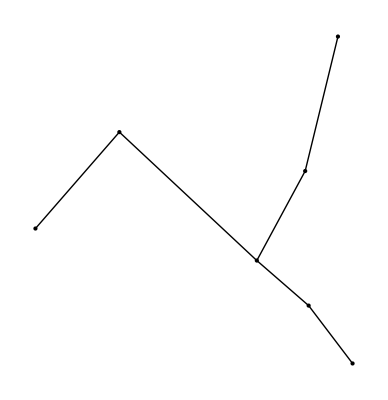

```mathematica
Graphics[{Map[Point,data1],line}]
```

連結行列 (MSTの情報より連結可能なパスが唯一のバスなので連結可能なパスを調べれば良い):

```mathematica
(conj={
{0,3,3,1,1,2,2},
{3,0,4,2,4,3,1},
{3,4,0,2,4,1,3},
{1,2,2,0,2,1,1},
{1,4,4,2,0,3,3},
{2,3,1,1,3,0,2},
{2,1,3,1,3,2,0}})//MatrixForm
```

(0 | 3 | 3 | 1 | 1 | 2 | 2
3 | 0 | 4 | 2 | 4 | 3 | 1
3 | 4 | 0 | 2 | 4 | 1 | 3
1 | 2 | 2 | 0 | 2 | 1 | 1
1 | 4 | 4 | 2 | 0 | 3 | 3
2 | 3 | 1 | 1 | 3 | 0 | 2
2 | 1 | 3 | 1 | 3 | 2 | 0)

```mathematica
(conjMat=conjMatFromAdjE[pos])//MatrixForm
```

(0 | 3 | 3 | 1 | 1 | 2 | 2
3 | 0 | 4 | 2 | 4 | 3 | 1
3 | 4 | 0 | 2 | 4 | 1 | 3
1 | 2 | 2 | 0 | 2 | 1 | 1
1 | 4 | 4 | 2 | 0 | 3 | 3
2 | 3 | 1 | 1 | 3 | 0 | 2
2 | 1 | 3 | 1 | 3 | 2 | 0)

```mathematica
conjMat==conj
```

True

クラス分けリスト:

:最初:

```mathematica
getMaxEdge[mst]:=mst[[Ordering[mst,1,(#1[[3]]>#2[[3]])&]]][[1]][[{1,2}]]
```

```mathematica
e[1]=getMaxEdge[mst]
```

{4,7}

```mathematica
makeFirstGr[edge_List,len_]:=Table[edge[[1]],{len}]
```

```mathematica
g[0]=makeFirstGr[getMaxEdge[mst],Length[conjMat]]
```

{4,4,4,4,4,4,4}

:1回目、エッジリストより最大距離[4-7]で切断:

```mathematica
(sedge=Sort[mst,(#1[[3]]>#2[[3]])&])//TableForm
```

4 | 7 | 0.486764
6 | 3 | 0.357918
7 | 2 | 0.330714
4 | 6 | 0.263111
1 | 5 | 0.18791
1 | 4 | 0.177653

```mathematica
Ordering[mst,1,(#1[[3]]>#2[[3]])&]
```

{5}

:グループの判定、ステップが近い方のグループに書き換える:

```mathematica
getGroupBySortedEdge[sedge_,pos_,conj_,prev_]:=Module[{edge,li,len,target,disc},
edge=sedge[[pos]][[{1,2}]];
li= Transpose[conj[[edge]]];
len=Length[prev];
target=Union[prev[[edge]]];
disc=Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li];
Table[If[prev[[n]]==target[[1]],disc[[n]],prev[[n]]],{n,len}]
]
```

```mathematica
getGroupByEdge[edge_,conj_,prev_]:=Module[{li,len,target,disc},
li= Transpose[conj[[edge]]];
len=Length[prev];
target=Union[prev[[edge]]];
disc=Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li];
Table[If[prev[[n]]==target[[1]],disc[[n]],prev[[n]]],{n,len}]
]
```

```mathematica
getGroupByEdge[edge_List,conj_]:=Module[{li,reprl},
li= Transpose[conj[[edge]]];
Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li]
(*reprl=Map[#->Null&,edge];*)
(*ReplacePart[Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li],reprl]*)
]
```

```mathematica
getGroupByEdge[edge_List,conj_,"Null"]:=Module[{li,reprl},
li= Transpose[conj[[edge]]];
(*Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li]*)
reprl=Map[#->Null&,edge];
ReplacePart[Map[If[#[[1]]<=#[[2]],edge[[1]],edge[[2]]]&,li],reprl]
]
```

```mathematica
g[0]
```

{4,4,4,4,4,4,4}

```mathematica
g[1]=getGroupBySortedEdge[sedge,1,conjMat,g[0]]
```

{4,7,4,4,4,4,7}

```mathematica
g[2]=getGroupBySortedEdge[sedge,2,conjMat,g[1]]
```

{6,7,3,6,6,6,7}

```mathematica
g[3]=getGroupBySortedEdge[sedge,3,conjMat,g[2]]
```

{6,2,3,6,6,6,7}

```mathematica
g[4]=getGroupBySortedEdge[sedge,4,conjMat,g[3]]
```

{4,2,3,4,4,6,7}

```mathematica
g[5]=getGroupBySortedEdge[sedge,5,conjMat,g[4]]
```

{1,2,3,1,5,6,7}

```mathematica
g[6]=getGroupBySortedEdge[sedge,6,conjMat,g[5]]
```

{1,2,3,4,5,6,7}

```mathematica
sedge//TableForm
```

4 | 7 | 0.486764
6 | 3 | 0.357918
7 | 2 | 0.330714
4 | 6 | 0.263111
1 | 5 | 0.18791
1 | 4 | 0.177653

:グループを作成:

```mathematica
makeEdgeGroup[gr_List,smst_]:=Module[{grIDs,mstEd,targetGr,cluster,edClass},
grIDs=Union[gr];
mstEd=Map[Drop[#,-1]&,smst];
targetGr=ReplacePart[gr,Map[{#}&,grIDs]->Null];
cluster=Map[Flatten[Position[targetGr,#]]&,grIDs];
(*Map[Position[mstEd,#][[1,1]]&,cluster[[2]]]*)
edClass=Table[Union[Map[Position[mstEd,#][[1,1]]&,cluster[[n]]]],{n,Length[cluster]}];
{Map[mst[[#]]&,edClass],targetGr}
]
```

```mathematica
mstgr=.
```

```mathematica
mstgr[1]=makeEdgeGroup[g[1],mst]
```

{{{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111},{6,3,0.357918}},{{7,2,0.330714}}},{4,7,4,Null,4,4,Null}}

```mathematica
makeEdgeGroup[g[2],mstgr[1][[2]]]
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[4, -1].

Drop::normal: Nonatomic expression expected at position 1 in Drop[7, -1].

Drop::normal: Nonatomic expression expected at position 1 in Drop[4, -1].

General::stop: Further output of Drop :: normal will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pkspec1: The expression {1, {} ⟦ 1, 1 ⟧} cannot be used as a part specification.

Part::pkspec1: The expression {{} ⟦ 1, 1 ⟧} cannot be used as a part specification.

{{{},{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111},{6,3,0.357918},{4,7,0.486764},{7,2,0.330714}}⟦{1,{}⟦1,1⟧}⟧,{{1,4,0.177653},{1,5,0.18791},{4,6,0.263111},{6,3,0.357918},{4,7,0.486764},{7,2,0.330714}}⟦{{}⟦1,1⟧}⟧},{6,7,Null,6,6,Null,Null}}

```mathematica
mst//TableForm
```

1 | 4 | 0.177653
1 | 5 | 0.18791
4 | 6 | 0.263111
6 | 3 | 0.357918
4 | 7 | 0.486764
7 | 2 | 0.330714

CVI評価:

:CVIの入力形式に変換:

:CVI評価:

::プログラム:
/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt

```mathematica
(*Get["/Users/kouamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]*)
```

```mathematica
Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]
```

Get::noopen: Cannot open "/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt".

$Failed

```mathematica
??mstPi2rkS
```

Information::notfound: Symbol "mstPi2rkS" not found.